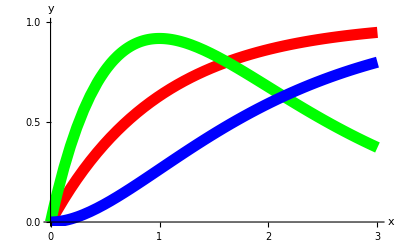

```mathematica
fgB=Plot[{1-E^-x,2.5x*E^{-x},1-E^-x*(1+x)},{x,0,3},PlotStyle->{{Red,Thickness[0.02]},{Green,Thickness[0.02]},{Blue,Thickness[0.02]}},Ticks->{Range[0,3,1],{{0,"0.0"},{0.5,"0.5"},{1,"1.0"}}},TicksStyle->{{FontSize->50,Bold},{FontSize->50,Bold}},AxesOrigin->{0,Automatic},PlotRange->{{0,3},{0,1}},
AxesStyle->{Directive[Black,50],Directive[Black,50]},AxesLabel->{Style["x",FontSize->50,Bold],Style["y",FontSize->50,Bold]}]
```

```mathematica
Export["/home/rafa/NetBeansProjects/DAMQT_2.0/images/plot2D.png", fgB,"PNG",ImageSize->300]
```

/home/rafa/NetBeansProjects/DAMQT_2.0/images/plot2D.png